# Practical - 1

## To solve 1st Order Linear differential equation and plotting its graph for particular solution

## Question - 1 : y'[x]+ 2*y[x]*Sin[2x]==2*ⅇ^Cos[2x]

{{y[x]→2 ⅇ^Cos[2 x] x+ⅇ^Cos[2 x] C[1]}}

{{y[x]→2 ⅇ^Cos[2 x] x}}

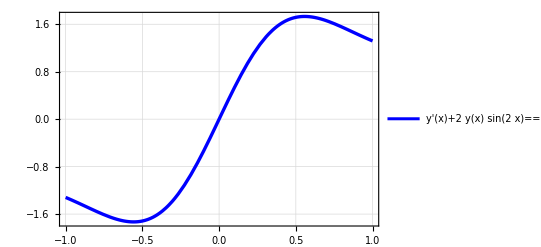

```mathematica
DSolve[{y'[x]+ 2*y[x]*Sin[2x]==2*ⅇ^Cos[2x]},y[x],x]
sol1 =DSolve[{y'[x]+ 2*y[x]*Sin[2x]==2*ⅇ^Cos[2x], y[0]==0},y[x],x]
Plot[y[x]/.sol1,{x,-1,1},PlotLegends->{y'[x]+ 2*y[x]*Sin[2x]==2*ⅇ^Cos[2x]},PlotStyle->{{Blue,Thickness[0.006]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question -2 : y'[x]+y[x]/x==y[x]*Log[x]

y[x]/x+y'[x]==Log[x] y[x]

{{y[x]→(ⅇ^(-x+x Log[x]) C[1])/x}}

{{y[x]→9/64 ⅇ^(4-x) x^(-1+x)}}

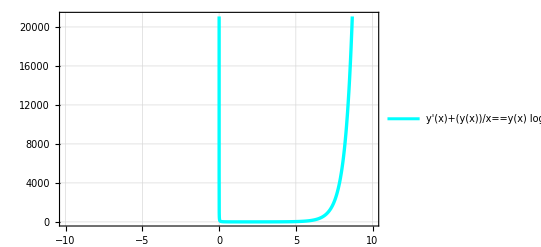

```mathematica
eq1=y'[x]+y[x]/x==y[x]*Log[x]
DSolve[{y'[x]+y[x]/x==y[x]*Log[x]},y[x],x]
sol2 = DSolve[{y'[x]+y[x]/x==y[x]*Log[x],y[4]==9},y[x],x]
Plot[y[x]/.sol2, {x,-10,10},PlotLegends->{eq1},PlotStyle->{{Cyan,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 3 : y’[x] * Tan[x] == 2*y[x] -8

Tan[x] y'[x]==-8+2 y[x]

{{y[x]→4+C[1] Sin[x]^2}}

{{y[x]→-4 (-1+Sin[x]^2)}}

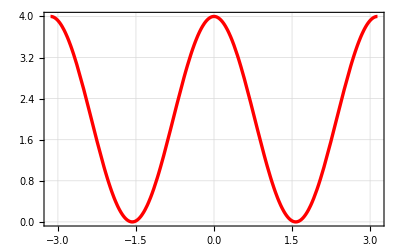

```mathematica
eq1=y'[x] * Tan[x] == 2*y[x] -8
DSolve[{y'[x] * Tan[x] == 2*y[x] -8} , y[x],x]
Sol3 = DSolve[{y'[x] * Tan[x] == 2*y[x] -8, y[π/2]== 0} , y[x],x]
Plot[y[x]/.Sol3, {x,-π,π},PlotStyle->{{Red,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],PlotStyle->{{Red,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 4: y'[x] == -((1+y[x]*ⅇ^x)/(x* ⅇ^x))

y'[x]==-(ⅇ^-x (1+ⅇ^x y[x]))/x

{{y[x]→ⅇ^-x/x+C[1]/x}}

{{y[x]→(ⅇ^(-3-x) (ⅇ^3-ⅇ^x+6 ⅇ^(3+x)))/x}}

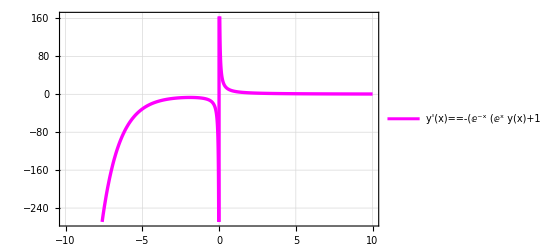

```mathematica
eq1= y'[x] == -((1+y[x]*ⅇ^x)/(x* ⅇ^x))
sol4 = DSolve[{y'[x] == -((1+y[x]*ⅇ^x)/(x* ⅇ^x))}, y[x],x]
sol4 = DSolve[{y'[x] == -((1+y[x]*ⅇ^x)/(x* ⅇ^x)), y[3]==2}, y[x],x]
Plot[y[x]/.sol4,{x,-10,10},PlotLegends->{eq1},PlotStyle->{{Magenta,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 5: y’[x]-y[x]*Tan[x]==-y[x]*Sec[x]

-Tan[x] y[x]+y'[x]==-Sec[x] y[x]

{{y[x]→C[1]/(Cos[x/2]+Sin[x/2])^2}}

{{y[x]→9/(Cos[x/2]+Sin[x/2])^2}}

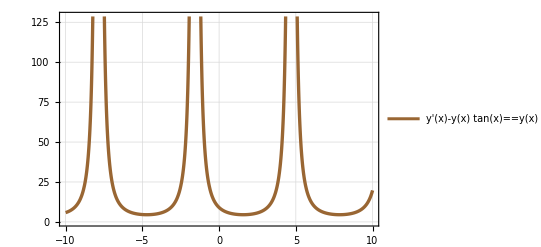

```mathematica
eq1=y'[x]-y[x]*Tan[x]==-y[x]*Sec[x]
DSolve[{y'[x]-y[x]*Tan[x]==-y[x]*Sec[x]},y[x],x]
sol5= DSolve[{y'[x]-y[x]*Tan[x]==-y[x]*Sec[x],y[0]==9},y[x],x]
Plot[y[x]/.sol5,{x,-10,10},PlotLegends->{eq1},PlotStyle->{{Brown,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

{{y[x]→-ⅇ^-x+C[1]}}

{{y[x]→ⅇ^-x (-1+ⅇ^x)}}

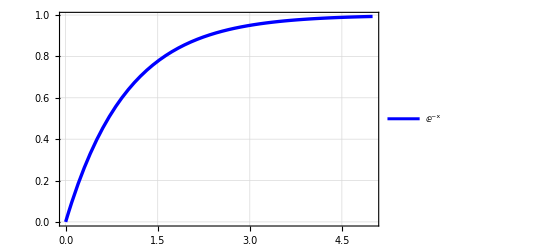

```mathematica
DSolve[{y'[x] == ⅇ^(-x)},y[x],x]
sol1 =DSolve[{y'[x] == ⅇ^(-x), y[0]==0},y[x],x]
Plot[y[x]/.sol1,{x,0,5},PlotLegends->{y'[x] = ⅇ^(-x)},PlotStyle->{{Blue,Thickness[0.006]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

```mathematica
DSolve[{y'[x] == ⅇ^-x},y[x],x]
```

{{y[x]→-ⅇ^-x+C[1]}}

```mathematica
DSolve[{True},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True}.

DSolve[{True},y[x],x]